```mathematica
ClearAll["Global`*"]
```

```mathematica
table051 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,5_1.txt",{"Table", "Data"}];
table051[[All,1]]=table051[[All,1]]-table051[[1,1]];
table051[[All,2]]=((table051[[All,2]]+0.002)/(0.0043×0.02408));
table051[[All,2]]=table051[[All,2]]-Min[table051[[All,2]]];
```

```mathematica
table052 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,5_2.txt",{"Table", "Data"}];
table052[[All,1]]=table052[[All,1]]-table052[[1,1]];
table052[[All,2]]=((table052[[All,2]]+0.002)/(0.0043×0.02408));
table052[[All,2]]=table052[[All,2]]-Min[table052[[All,2]]];
```

```mathematica
table053 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,5_3.txt",{"Table", "Data"}];
table053[[All,1]]=table053[[All,1]]-table053[[1,1]];
table053[[All,2]]=((table053[[All,2]]+0.002)/(0.0043×0.02408));
table053[[All,2]]=table053[[All,2]]-Min[table053[[All,2]]];
```

```mathematica
table054 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,5_4.txt",{"Table", "Data"}];
table054[[All,1]]=table054[[All,1]]-table054[[1,1]];
table054[[All,2]]=((table054[[All,2]]+0.002)/(0.0043×0.02408));
table054[[All,2]]=table054[[All,2]]-Min[table054[[All,2]]];
```

```mathematica
table055 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,5_5.txt",{"Table", "Data"}];
table055[[All,1]]=table055[[All,1]]-table055[[1,1]];
table055[[All,2]]=((table055[[All,2]]+0.002)/(0.0043×0.02408));
table055[[All,2]]=table055[[All,2]]-Min[table055[[All,2]]];
```

```mathematica
T[k_,T0_,Tout_,t_]:=Tout+(T0-Tout)×Exp[-k×t]
```

```mathematica
fit051=FindFit[table051,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.257525,T0→20.5712,Tout→-1.17752}

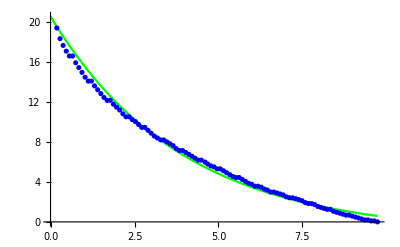

```mathematica
Show[Plot[T[k,T0,Tout,t]/.fit051,{t,0,Max[table051[[All,1]]]},PlotStyle->Green],ListPlot[table051,PlotStyle->Blue]]
```